```mathematica
Exit[]
```

```mathematica
$Assumptions={_∈Reals, X0[x]∈Reals,Y0[x]∈Reals,aa>0,κ>0,β>0,Δ>0,lp>0,ϵ>0,λ[1]>0,λ[2]>0,λ[3]>0,Q1>0, μ>0,μ1>0,μ2>0,μ3>0,Δ>0,η>0,Px[x1]>0,Py[x1]>0,-3 K0[t]^2+Λ P0[t]<0,P0[t]>0,Sin[θ]>0};
```

## Kretschmann vs Rs

```mathematica
Get[NotebookDirectory[]<>"eoms.wl"];
Needs["DifferentialEquations`NDSolveProblems`"];
Needs["DifferentialEquations`NDSolveUtilities`"];
```

```mathematica
bdy0={Ex[x0]-> 3/2 (3/2)^(1/3) (√Rs (x0))^(4/3),Eϕ[x0]-> (3/2)^(1/3) √Rs (√Rs (x0))^(1/3),Kx[x0]-> Rs/(3 2^(2/3) 3^(1/3) (√Rs (x0))^(4/3)),Kϕ[x0]-> -((2/3)^(1/3) √Rs)/(√Rs (x0))^(1/3)};bdyKv0=Refine[{K1[z]-> (√Ex[z] Kx[z])/Eϕ[z],K2[z]-> Kϕ[z]/(√Ex[z]),v1[z]-> Log[Ex[z]],v2[z]-> Log[Eϕ[z]]}/.z-> x0/.bdy0,Assumptions->{x0>0,Δ>0,Rs>0}];
bdyKv={K1[z]==K1[x0],K2[z]==K2[x0],v1[z]==v1[x0],v2[z]==v2[x0]}/.bdyKv0/.z-> x0
```

{K1[x0]==1/(6 x0),K2[x0]==-2/(3 x0),v1[x0]==Log[3/2 (3/2)^(1/3) Rs^(2/3) x0^(4/3)],v2[x0]==Log[(3/2)^(1/3) Rs^(2/3) x0^(1/3)]}

```mathematica
bdyKv/.parameters//N
```

{K1[3.×10^8]==5.55556×10^-10,K2[3.×10^8]==-2.22222×10^-9,v1[3.×10^8]==40.3819,v2[3.×10^8]==20.4571}

```mathematica
xM=3*10^8;
m=21;
parameters={a-> 1,β->1,Rs->10^7 m,Δ->0.1,t0->0,x0-> xM,μ0-> 0.1,λ0-> 0.1};
effeomODEKv={Table[eomKv[[i]]==0,{i,1,4}],bdyKv}/.parameters//Flatten;
nsolKv=NDSolve[effeomODEKv,{K1[z],K2[z],v1[z],v2[z]},{z,-600,xM},Method->"ImplicitRungeKutta"]//Flatten
```

{K1[z]→InterpolatingFunction[…][z],K2[z]→InterpolatingFunction[…][z],v1[z]→InterpolatingFunction[…][z],v2[z]→InterpolatingFunction[…][z]}

General::munfl: Exp[-1158.62] is too small to represent as a normalized machine number; precision may be lost.

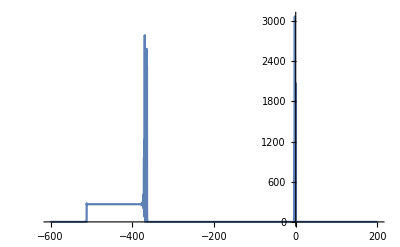

```mathematica
KretschmannN2=(Kretschmann/.{x-> t+z}/.chvarearly/.D[chvarearly, z]//Simplify)/.parameters/.nsolKv/.D[nsolKv, z]/.D[D[nsolKv, z], z];
Plot[KretschmannN2,{z,-600,200},PlotRange->All]
```

```mathematica
gap=0.00001;
KrR[m]={Max[ParallelTable[KretschmannN2,{z,-380,-360,gap}]],Max[ParallelTable[KretschmannN2,{z,-10,10,gap}]]}//AbsoluteTiming
```

{977.841,{5186.9,5912.94}}

```mathematica
KretschmannR=Table[KrR[i][[2]],{i,1,m}]
```

{{4624.8,5888.92},{4776.16,5951.41},{4842.81,5889.28},{4893.4,5926.99},{4952.36,5924.66},{4988.82,5943.48},{4969.07,5920.37},{4993.14,5898.8},{5043.08,5903.97},{5075.1,5913.2},{5054.17,5918.56},{5102.26,5883.77},{5114.5,5951.31},{5099.82,5911.32},{5108.38,5917.9},{5135.23,5906.79},{5146.73,5951.36},{5128.95,5911.31},{5137.62,5911.25},{5180.83,5945.37},{5186.9,5912.94}}

```mathematica
Save[NotebookDirectory[]<>"KretschmannVsRs(xM=3*10^8,Rs->m*10^7,m=1--21,Delta->0.1,the second column is for the bounce at z=0).wl",KretschmannR]
```

```mathematica
KretschmannR1=Table[KretschmannR[[i,1]],{i,1,m}]
```

{4624.8,4776.16,4842.81,4893.4,4952.36,4988.82,4969.07,4993.14,5043.08,5075.1,5054.17,5102.26,5114.5,5099.82,5108.38,5135.23,5146.73,5128.95,5137.62,5180.83,5186.9}

```mathematica
KretschmannR2=Table[KretschmannR[[i,2]],{i,1,m}]
```

{5888.92,5951.41,5889.28,5926.99,5924.66,5943.48,5920.37,5898.8,5903.97,5913.2,5918.56,5883.77,5951.31,5911.32,5917.9,5906.79,5951.36,5911.31,5911.25,5945.37,5912.94}

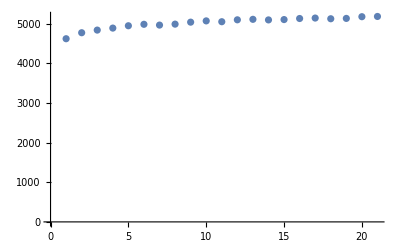

```mathematica
ListPlot[KretschmannR1,AxesOrigin->{0,0}]
```

```mathematica
LinearModelFit[Transpose[{Table[10^7 i,{i,1,Length[KretschmannR1]}],KretschmannR1}],x,x]
```

FittedModel[4794.73+2.10596×10^-6 x]

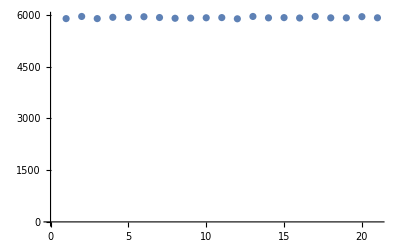

```mathematica
ListPlot[KretschmannR2,AxesOrigin->{0,0}]
```

```mathematica
LinearModelFit[Transpose[{Table[10^7 i,{i,1,Length[KretschmannR2]}],KretschmannR2}],x,x]
```

FittedModel[5913.64+4.17673×10^-8 x]